```mathematica
Clear["Global`*"]
```

```mathematica
metaFile = FileNameJoin[{NotebookDirectory[],"meta.dat"}];
rhoFile = FileNameJoin[{NotebookDirectory[],"rho.dat"}];
uFile = FileNameJoin[{NotebookDirectory[],"u.dat"}];
TFile = FileNameJoin[{NotebookDirectory[],"T.dat"}];
```

```mathematica
Ns = BinaryRead[metaFile,"UnsignedInteger32"]
Nt = BinaryRead[metaFile,"UnsignedInteger32"]+1
ds = BinaryRead[metaFile,"Real32"]
dt = BinaryRead[metaFile,"Real32"]
Δchr=BinaryRead[metaFile,"Real64"]
Close[metaFile];
```

1024

1000

6.15234×10^6

0.004

5.×10^8

```mathematica
rho=BinaryReadList[rhoFile,"Real32"];
u = BinaryReadList[uFile,"Real32"];
T = BinaryReadList[TFile,"Real32"];
rho = ArrayReshape[rho, {Nt,Ns}];
u = ArrayReshape[u, {Nt,Ns}];
T = ArrayReshape[T, {Nt,Ns}];
```

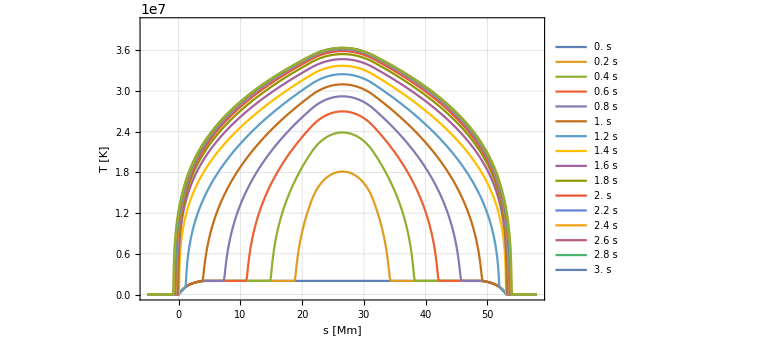

/home/byrdie/School/Classes/PHSX591_SolarFlaresAndCMEs/FinalProject/report/figures/temp_vs_time.eps

```mathematica
step = 50;
p1=ListLinePlot[T[[1;;Nt-IntegerPart[0.6/dt];;step]],PlotRange->{0,4 10^7},PlotTheme->"Detailed",DataRange->{-Δchr/10^8,(Ns ds - Δchr)/10^8},PlotLegends->{Table[t *dt Quantity[, "Seconds"],{t,0,Nt,step}]},ImageSize->Large,Frame->True,FrameLabel->{"s [Mm]","T [K]"}]
Export[FileNameJoin[{NotebookDirectory[],"temp_vs_time.eps"}],p1]
```

```mathematica
T1 = IntegerPart[3.5 / dt]
L1h = 2.8 10^8;
L1l=-1.75 10^8;
L1f=53 10^8/2 ;
S1h=(L1h+ Δchr)/ds //IntegerPart
S1l = ( L1l+ Δchr) /ds //IntegerPart
S1f = (L1f+ Δchr)/ds //IntegerPart
```

874

126

52

511

```mathematica
sz = 600
```

600

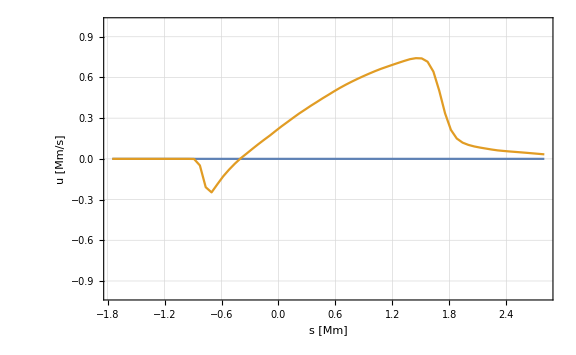

/home/byrdie/School/Classes/PHSX591_SolarFlaresAndCMEs/FinalProject/report/figures/vel_vs_s.eps

```mathematica
g11 = ListPlot[{u[[1,S1l;;S1h]]/10^8,u[[T1,S1l;;S1h]]/10^8},PlotRange->{-1,1},DataRange->{L1l/10^8,L1h/10^8},PlotTheme->"Detailed",Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"s [Mm]","u [Mm/s]"}]
Export[FileNameJoin[{NotebookDirectory[],"vel_vs_s.eps"}],g11]
```

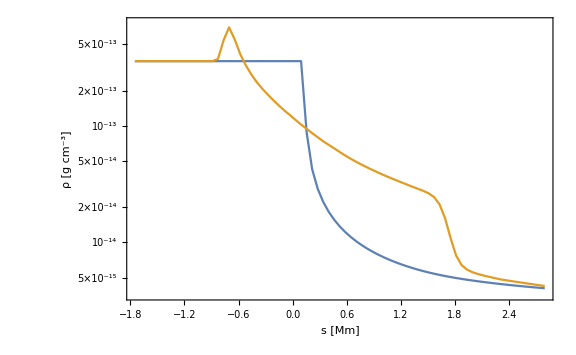

/home/byrdie/School/Classes/PHSX591_SolarFlaresAndCMEs/FinalProject/report/figures/rho_vs_s.eps

```mathematica
g21 = ListLogPlot[{rho[[1,S1l;;S1h]],rho[[T1,S1l;;S1h]]},PlotRange->{Min[rho],Max[rho]},DataRange->{L1l/10^8,L1h/10^8},Joined->True,Frame->True,FrameLabel->{"s [Mm]","ρ [g cm^-3]"},PlotTheme->"Detailed",ImageSize->Large]
Export[FileNameJoin[{NotebookDirectory[],"rho_vs_s.eps"}],g21]
```

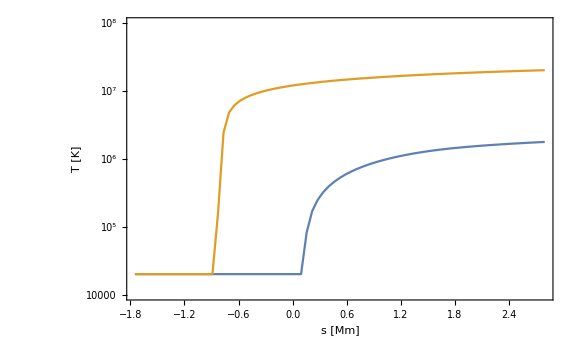

/home/byrdie/School/Classes/PHSX591_SolarFlaresAndCMEs/FinalProject/report/figures/T_vs_s.eps

```mathematica
g31 = ListLogPlot[{T[[1,S1l;;S1h]],T[[T1,S1l;;S1h]]},PlotRange->{10^4,10^8},DataRange->{L1l/10^8,L1h/10^8},Joined->True,Frame->True,FrameLabel->{"s [Mm]","T [K]"},PlotTheme->"Detailed",ImageSize->Large]
Export[FileNameJoin[{NotebookDirectory[],"T_vs_s.eps"}],g31]
```